{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

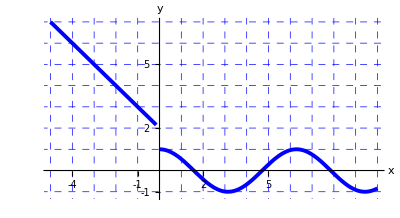

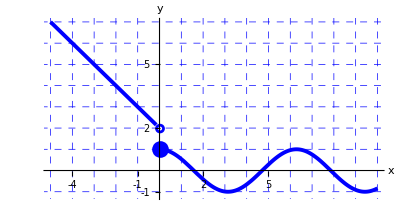

```mathematica
Clear[f,x];

f[x_] :=-x+2/;x<-0.15;
f[x_] :=Cos[x]/;0<x



xTicks=Table[n ,{n,-4,7}]
yTicks=Table[n,{n,-4,7}]
One=Plot[f[x],{x,-5,10},PlotRange->{-1.2,7},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Su=Graphics[{Blue,PointSize[0.03],Point[{0,1}]}];

Pe=Graphics[{Blue,Thickness[0.005],Circle[{0,2},0.16]}];

Show[One,Su,Pe]
```

```mathematica
Show[%99,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.98]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

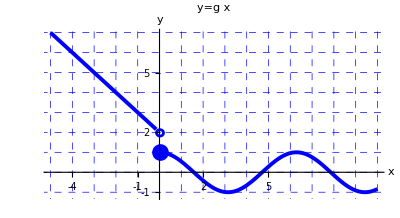

```mathematica
Show[%100,PlotLabel->HoldForm[y=g x],LabelStyle->{8,GrayLevel[0]}]
```

```mathematica
Show[%101,PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

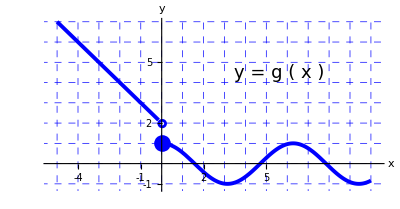

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

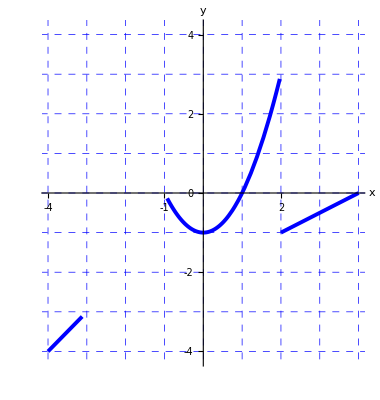

```mathematica
Clear[f,x];

f[x_] :=x/;-4<x<-3.12;
f[x_] :=x^2-1/;-0.93<x<1.97
f[x_] :=0.5(x-4)/;2<x<4

xTicks=Table[n ,{n,-4,7}]
yTicks=Table[n,{n,-4,7}]
One=Plot[f[x],{x,-4,4},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Su=Graphics[{Blue,PointSize[0.038],Point[{-4,-4}]}];
Ku=Graphics[{Blue,PointSize[0.038],Point[{-2,-2}]}];
Soo=Graphics[{Blue,PointSize[0.038],Point[{4,0}]}];
Kuu=Graphics[{Blue,PointSize[0.038],Point[{2,-1}]}];
So=Graphics[{Blue,PointSize[0.038],Point[{-3,0}]}];
Pe=Graphics[{Blue,Thickness[0.005],Circle[{-3,-3
},0.125]}];
Pee=Graphics[{Blue,Thickness[0.005],Circle[{-1,0
},0.125]}];
Se=Graphics[{Blue,Thickness[0.005],Circle[{2,3
},0.125]}];
Show[One,Su,So,Soo,Ku,Kuu,Pe,Se,Pee]
```

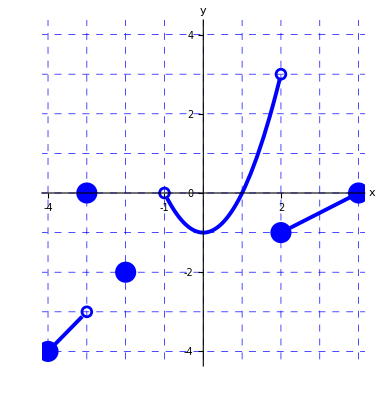

-Graphics-

```mathematica
Show[%504,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.995]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

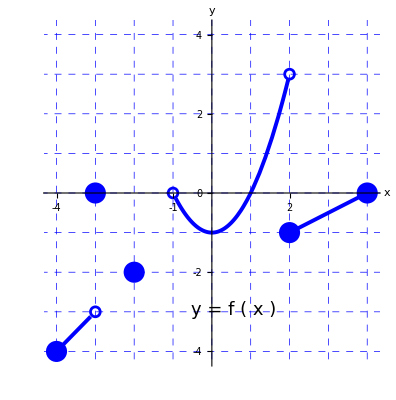

{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6}

{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6}

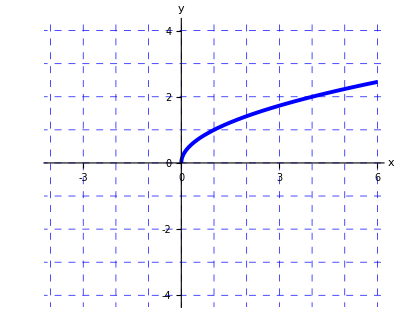

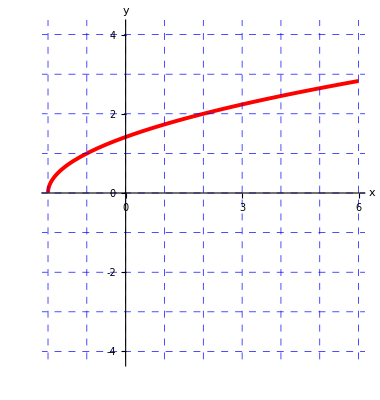

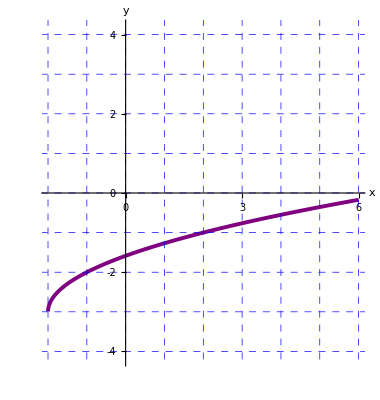

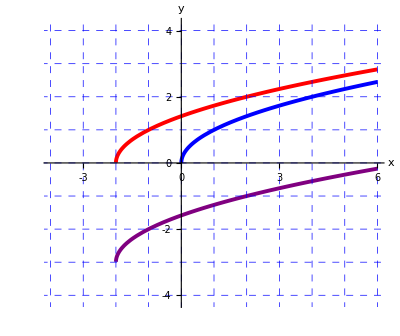

```mathematica
Clear[f,g,h,x];
f[x_] :=20/;x<-0.12;
f[x_] :=√x/;0<x;
g[x_] :=√(2+x)/;-2<x
g[x_] :=√(2+x)/;x<-2.1
h[x_] :=-3+√(2+x)/;-2<x
h[x_] :=-3+√(2+x)/;x<-2.1
xTicks=Table[n ,{n,-6,6}]
yTicks=Table[n,{n,-6,6}]
One=Plot[f[x],{x,-4,6},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-6,-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-6,-5,-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Onn=Plot[g[x],{x,-4,6},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Red,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-6,-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-6,-5,-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Onnn=Plot[h[x],{x,-4,6},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Purple,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-6,-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-6,-5,-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Show[One,Onn,Onnn]
```

```mathematica
Show[%649,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.11]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6}

{-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6}

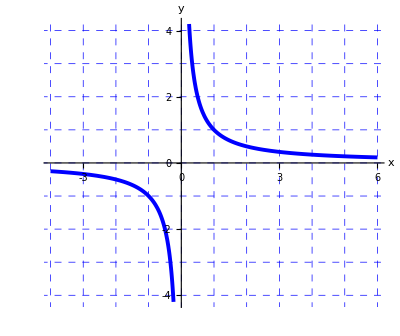

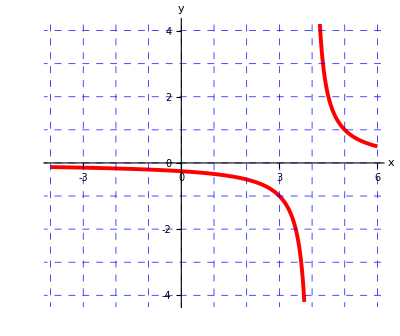

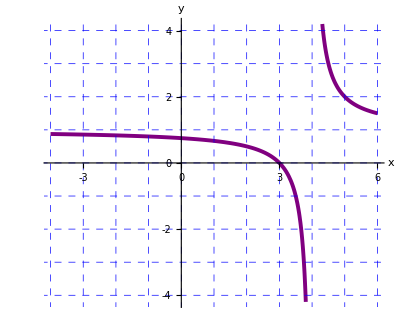

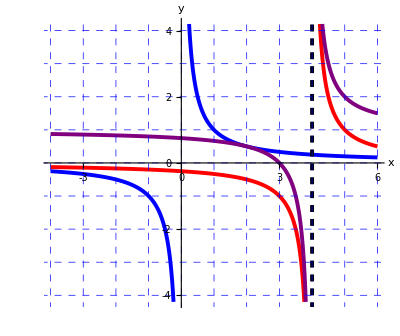

```mathematica
Clear[f,g,h,x];

f[x_] :=1/x/;-6<x<-0.1;
f[x_] :=1/x/;0.1<x;
g[x_] :=1/(x-4)/;-6<x<3.9
g[x_] :=1/(x-4)/;4.1<x

h[x_] :=1/(x-4)+1/;-6<x<3.9
h[x_] :=1/(x-4)+1/;4.1<x
xTicks=Table[n ,{n,-6,6}]
yTicks=Table[n,{n,-6,6}]
One=Plot[f[x],{x,-4,6},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-6,-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-6,-5,-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Onn=Plot[g[x],{x,-4,6},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Red,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-6,-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-6,-5,-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Onnn=Plot[h[x],{x,-4,6},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Purple,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-6,-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-6,-5,-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
linex=Graphics[{Black,Dashed,Thickness[0.007],Line[{{4,-6},{4,6}}]}];
Show[One,Onn,Onnn,linex]
```

```mathematica
Show[%715,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.975]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

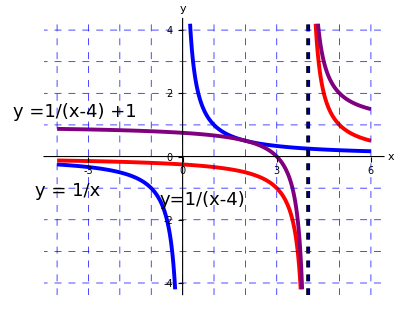

```mathematica
Show[%700,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.985]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

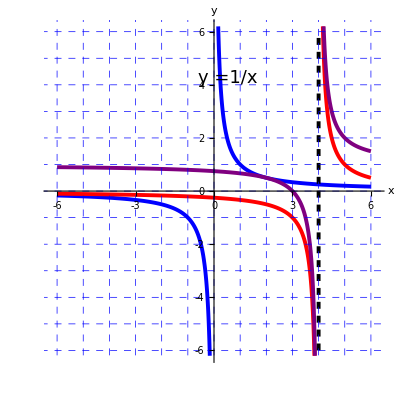

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

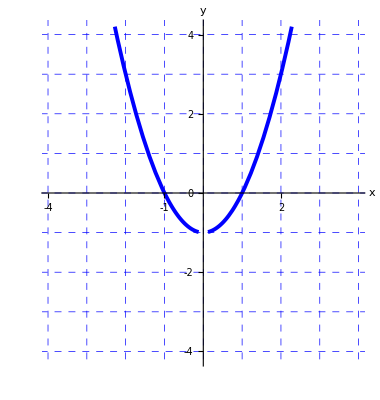

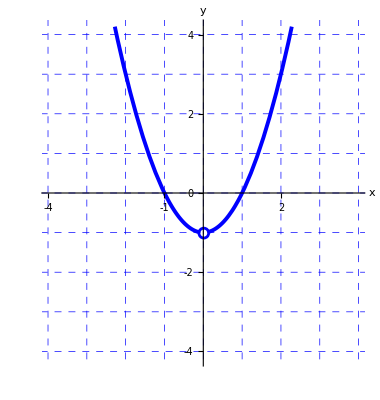

```mathematica
Clear[f,x];

f[x_] :=x^2-1/;-4<x<-0.12;
f[x_] :=x^2-1/;0.12<x<4


xTicks=Table[n ,{n,-4,7}]
yTicks=Table[n,{n,-4,7}]
One=Plot[f[x],{x,-4,4},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]

Pe=Graphics[{Blue,Thickness[0.005],Circle[{0,-1
},0.125]}];


Show[One,Pe]
```

```mathematica
Show[%740,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

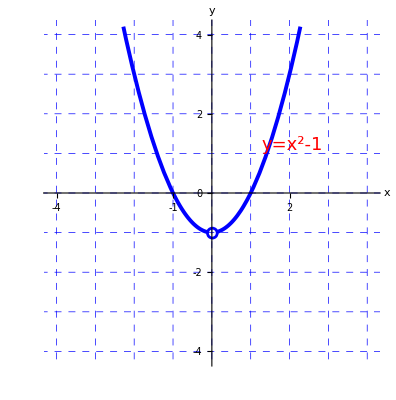

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

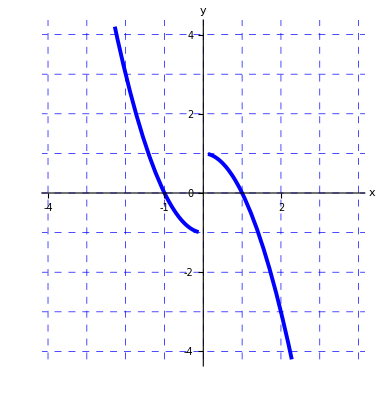

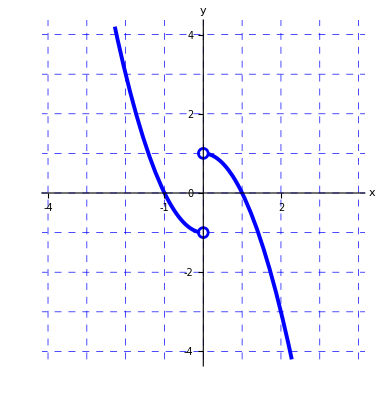

```mathematica
Clear[f,x];

f[x_] :=x^2-1/;-4<x<-0.12;
f[x_] :=1-x^2/;0.12<x<4


xTicks=Table[n ,{n,-4,7}]
yTicks=Table[n,{n,-4,7}]
One=Plot[f[x],{x,-4,4},PlotRange->{-4.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]

Pe=Graphics[{Blue,Thickness[0.005],Circle[{0,-1
},0.125]}];

Pee=Graphics[{Blue,Thickness[0.005],Circle[{0,1
},0.125]}];
Show[One,Pe,Pee]
```

```mathematica
Show[%750,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.98]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

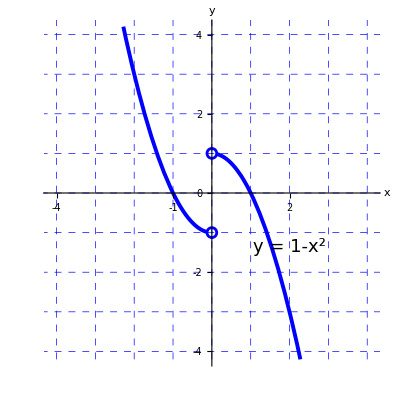

{-3,0,3}

{-160,-120,-80,-40,0,40,80,120,160}

-Graphics-

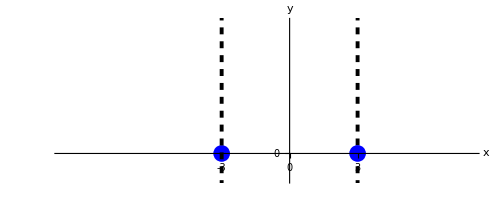

```mathematica
Clear[f,x];

f[x_] :=40/;x<8;




xTicks=Table[3n ,{n,-1,1}]
yTicks=Table[40n,{n,-4,4}]
One=Plot[f[x],{x,-10,10},PlotRange->{-1.2,6},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic]
Su=Graphics[{Blue,PointSize[0.03],Point[{-3,0}]}];
linex=Graphics[{Black,Dashed,Thickness[0.007],Line[{{-3,-6},{-3,8}}]}];
linexx=Graphics[{Black,Dashed,Thickness[0.007],Line[{{3,-6},{3,8}}]}];
Pe=Graphics[{Blue,PointSize[0.03],Point[{3,0}]}];

Show[One,Su,linex, linexx,Pe]
```

```mathematica
Show[%789,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.155]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

```mathematica
Show[%790,PlotLabel->None,LabelStyle->{14,GrayLevel[0]}]
```

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

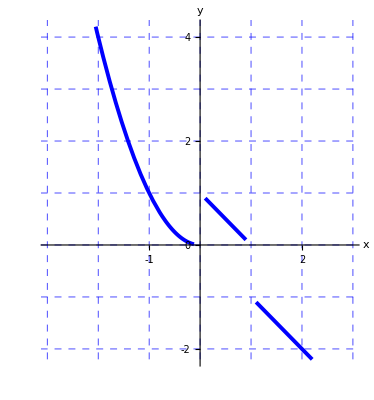

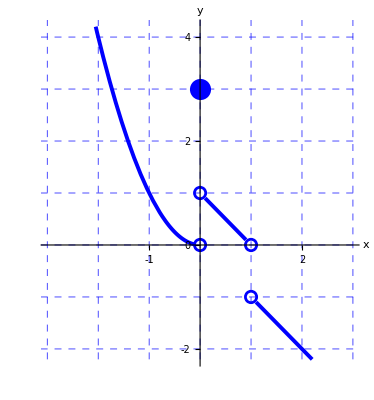

```mathematica
Clear[f,x];

f[x_] :=x^2/;-4<x<-0.12;
f[x_] :=1-x/;0.1<x<0.9
f[x_] :=-x/;1.1<x

xTicks=Table[n ,{n,-4,7}]
yTicks=Table[n,{n,-4,7}]
One=Plot[f[x],{x,-3,3},PlotRange->{-2.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Su=Graphics[{Blue,PointSize[0.038],Point[{0,3}]}];

Pe=Graphics[{Blue,Thickness[0.005],Circle[{0,1
},0.11]}];
Pee=Graphics[{Blue,Thickness[0.005],Circle[{0,0
},0.11]}];
Se=Graphics[{Blue,Thickness[0.005],Circle[{1,0
},0.11]}];
So=Graphics[{Blue,Thickness[0.005],Circle[{1,-1
},0.11]}];
Show[One,Su,So,Pe,Se,Pee]
```

```mathematica
Show[%872,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.09]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

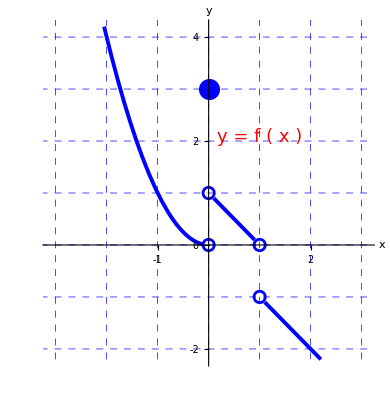

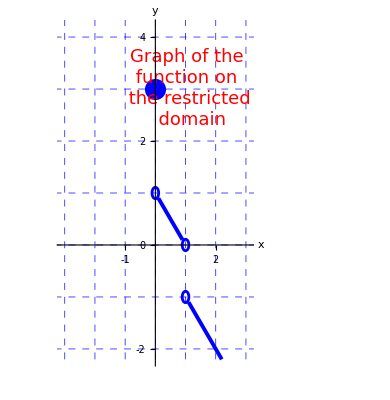

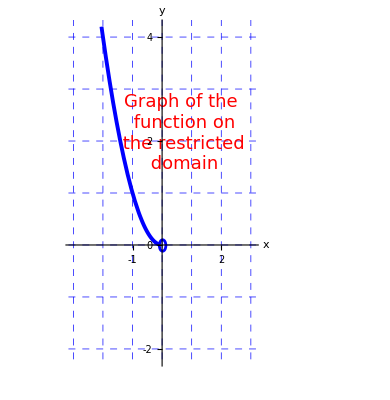

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

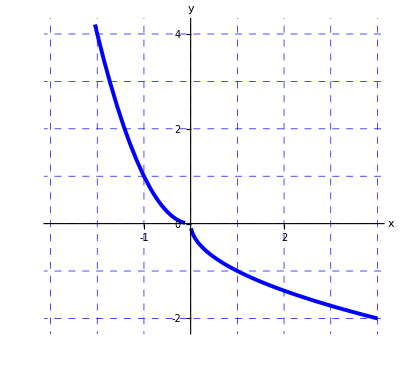

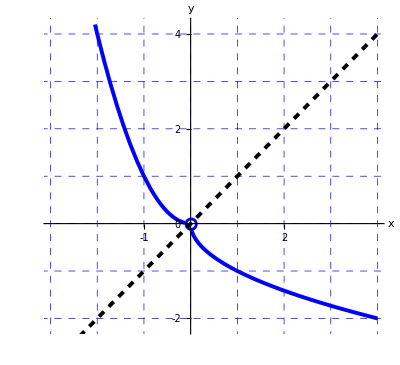

```mathematica
Clear[f,x];

f[x_] :=x^2/;-4<x<-0.12;
f[x_] :=-√x/;0.01<x


xTicks=Table[n ,{n,-4,7}]
yTicks=Table[n,{n,-4,7}]
One=Plot[f[x],{x,-3,4},PlotRange->{-2.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Su=Graphics[{Blue,PointSize[0.038],Point[{0,3}]}];
linex=Graphics[{Black,Dashed,Thickness[0.007],Line[{{-4,-4},{4,4}}]}];
Pe=Graphics[{Blue,Thickness[0.005],Circle[{0,1
},0.11]}];
Pee=Graphics[{Blue,Thickness[0.005],Circle[{0,0
},0.11]}];
Se=Graphics[{Blue,Thickness[0.005],Circle[{1,0
},0.11]}];
So=Graphics[{Blue,Thickness[0.005],Circle[{1,-1
},0.11]}];
Show[One,Pee,linex]
```

```mathematica
Show[%983,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[0.9550000000000001]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

{-4,-3,-2,-1,0,1,2,3,4,5,6,7}

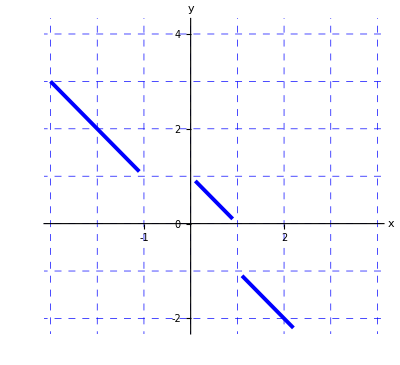

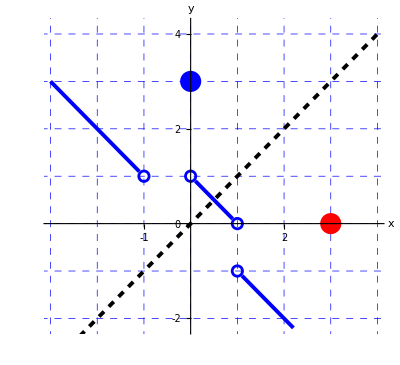

```mathematica
Clear[f,x];

f[x_] :=-x/;-4<x<-1.1;

f[x_] :=1-x/;0.1<x<0.9
f[x_] :=-x/;1.1<x

xTicks=Table[n ,{n,-4,7}]
yTicks=Table[n,{n,-4,7}]
One=Plot[f[x],{x,-3,4},PlotRange->{-2.2,4.2},Ticks->{xTicks,yTicks},
    PlotStyle->{{Blue,Thickness[0.007]}},AxesLabel->{"x","y"}, AspectRatio-> Automatic,GridLines-> {{-5,-4, -3, -2, -1,0,1,2,3,4,5,6,7,8,9,10},{-4,-3,-2,-1,0,1,2, 3, 4, 5,6,7}},GridLinesStyle-> Directive[Blue,Dashed]]
Su=Graphics[{Blue,PointSize[0.038],Point[{0,3}]}];
Suu=Graphics[{Red,PointSize[0.038],Point[{3,0}]}];
linex=Graphics[{Black,Dashed,Thickness[0.007],Line[{{-4,-4},{4,4}}]}];
Pe=Graphics[{Blue,Thickness[0.005],Circle[{0,1
},0.11]}];
Pee=Graphics[{Blue,Thickness[0.005],Circle[{-1,1
},0.11]}];
Se=Graphics[{Blue,Thickness[0.005],Circle[{1,0
},0.11]}];
So=Graphics[{Blue,Thickness[0.005],Circle[{1,-1
},0.11]}];
Show[One,Su,Suu,So,Pe,Se,Pee,linex]
```

```mathematica
Show[%1029,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.025]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({({{Identity,Identity},{Identity,Identity}}⟦1,2⟧[#1]&)[#1⟦1⟧],({{Identity,Identity},{Identity,Identity}}⟦2,2⟧[#1]&)[#1⟦2⟧]}&)}}]
```